```mathematica
(* materials: https://arxiv.org/pdf/1901.11457 , https://github.com/JarekDuda/SGD-OGR-Hessian-estimator/ *)
```

```mathematica
(* basic step in d dimensional subspace, using ng: noisy gradient in θ *)
sOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);     (* means *)
V=Orthogonalize[Table[v+Γ*ng,{v,V}]];   (* explore new directions *)
pθ=V.(θ-mθ);pg=V.(ng-mg);       (* mean subtractions & projections *)
θ-=α(m-m.Transpose[V].V);       (* momentum in remaining  directions *)                                                       
mθθ+=β(KroneckerProduct[pθ,pθ]-mθθ); {e,ev}=Eigensystem[mθθ];
mgθ+=β(KroneckerProduct[pg,pθ]-mgθ); evt=Transpose[ev];
pH=evt.((ev.s[mgθ].evt)/s[Table[e,d]]).ev;   (* Hessian estimator *) 
θ-=(ma[pH].(V.m)).V);      (* 1/|~eigenvalues of pH| in local subspace *)

eh[lm_]:=1/Map[Max[#,cut]&,Abs[lm]*div]; (* eigenvalue inv, div&cut *)
ma[A_]:=({e,ev}=Eigensystem[A];Transpose[ev].DiagonalMatrix[eh[e]].ev);
init[d_]:=(m=mg=mθ=dgθ=Table[0.,𝔇];V=RandomReal[0.001,{d,𝔇}];
dθθ=Table[1.,𝔇];mgθ=Table[0.,d,d];mθθ=IdentityMatrix[d];);
noise:=RandomReal[NormalDistribution[0,ϵ],𝔇];ϵ=0.1;   (*Gaussian noise*)
b=(1.5-x+x*y)^2+(2.25-x+x*y^2)^2+(2.625-x+x*y^3)^2;(* Beale function *)
f=Simplify[b+(b/.x->z)];v={x,y,z};𝔇=Length[v];(*3D:b(x,y)+b(z,y)*)
sub[p_]:=Table[v[[i]]->p[[i]],{i,𝔇}]; s[M_]:=M+Transpose[M];
g=Grad[f,v];H=Table[D[f,v1,v2],{v1,v},{v2,v}]; (*gradient,Hessian *)
α=0.001;β=0.6;γ=0.6;div=1.5;Γ=0.25;cut=10;     (* hyperparameters *) 
d=2; init[d]; θ={0,0,0};   (* dimension, initialize, starting position *)
steps=50;Do[sOGR[(g/.sub[θ])+noise],{i,steps}];       (* optimization *)
steps=50;r=3; seed=1;   (* global testing parametrs *)
f/.sub[θ]
```

0.000379608

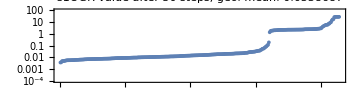

```mathematica
fv={};β=0.6;γ=0.7;Γ=0.1;div=1.5;cut=15;SeedRandom[seed];d=1;(* d=1 dim. subspace *)
paths=Table[init[d];θh={}; θ={sx,sy,sz};  (*starting position *)
Do[AppendTo[θh,θ];sOGR[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-r,r},{sy,-r,r},{sz,-r,r}];
ListLogPlot[s1OGRp=Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"s1OGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

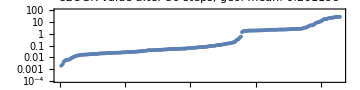

```mathematica
fv={};β=0.6;γ=0.9;Γ=0.2;div=4.;cut=20;SeedRandom[seed];d=2;(* d=2 dim. subspace *)
paths=Table[init[d];θh={}; θ={sx,sy,sz};  (*starting position *)
Do[AppendTo[θh,θ];sOGR[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-r,r},{sy,-r,r},{sz,-r,r}];
ListLogPlot[s2OGRp=Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"s2OGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

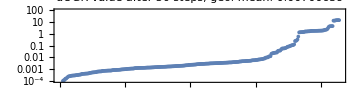

```mathematica
dOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);    (* means *)
dθθ+=β((θ-mθ)^2-dθθ);dgθ+=β((ng-mg)*(θ-mθ)-dgθ); (*coord.*)
θ-=1/Map[Max[#,cut]&,Abs[dgθ/dθθ]*div]*m);   (*1/|1D λ div&cut|*)
(* equivalently : θ-=eh[dgθ/dθθ]*m *)

fv={};β=0.6;γ=0.7;div=1.4;cut=5;SeedRandom[1];
paths=Table[init[𝔇];θh={}; θ={sx,sy,sz};  (*starting position *)
Do[AppendTo[θh,θ];dOGR[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-r,r},{sy,-r,r},{sz,-r,r}];
ListLogPlot[dOGRp=Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"dOGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

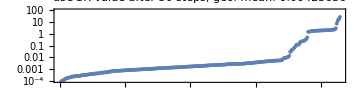

```mathematica
dsOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);     (* means *)
dθθ+=β((θ-mθ)^2-dθθ);dgθ+=β((ng-mg)*(θ-mθ)-dgθ); (* d Hessian *)
V=Orthogonalize[Table[v+Γ*ng,{v,V}]];   (* explore new directions *)
pθ=V.(θ-mθ);pg=V.(ng-mg);       (* mean subtractions & projections *)                                                 
mθθ+=β(KroneckerProduct[pθ,pθ]-mθθ); {e,ev}=Eigensystem[mθθ];
mgθ+=β(KroneckerProduct[pg,pθ]-mgθ); evt=Transpose[ev];
pH=evt.((ev.s[mgθ].evt)/s[Table[e,d]]).ev;   (* Hessian estimator *) 
Δθ=eh[dgθ/dθθ]*m;θ-=Δθ-w(Δθ.Transpose[V].V-(ma[pH].(V.m)).V));

fv={};β=0.6;γ=0.7;div=1.5;Γ=0.1;cut=6;w=0.4;SeedRandom[1];d=2;(* d=2 dim. subspace *)
paths=Table[init[d];θh={}; θ={sx,sy,sz};  Do[AppendTo[θh,θ];dsOGR[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-r,r},{sy,-r,r},{sz,-r,r}];
ListLogPlot[ds2OGRp=Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"dsOGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

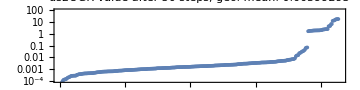

```mathematica
fv={};β=0.6;γ=0.7;Γ=0.1;div=1.5;cut=6;w=0.3;SeedRandom[1];d=1;(* d=1 dim. subspace *)
paths=Table[init[d];θh={}; θ={sx,sy,sz};  Do[AppendTo[θh,θ];dsOGR[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-r,r},{sy,-r,r},{sz,-r,r}];
ListLogPlot[ds1OGRp=Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"ds2OGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

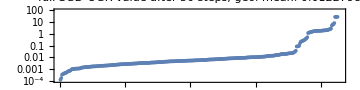

```mathematica
(* fOGR: full OGR *)
fOGR[ng_]:=(m+=γ(ng-m);                                  (* update momentum, averages: *)
mθ+=β(θ-mθ);mθθ+=β(KroneckerProduct[θ-mθ,θ-mθ]-mθθ);
mg+=β(ng-mg);mgθ+=β(KroneckerProduct[ng-mg,θ-mθ]-mgθ);
mgθs=mgθ+Transpose[mgθ];{e,ev}=Eigensystem[mθθ];
pH=Transpose[ev].((ev.mgθs.Transpose[ev])/
(Table[e,𝔇]+Transpose[Table[e,𝔇]])).ev;      (* Hessian estimator *) 
θ-=ma[pH].m);                        (* 1/|~eigenvalues of pH: predicted Hessian| *)

fv={};β=0.5;γ=0.6;div=1.5;cut=10;SeedRandom[1];
paths=Table[init[𝔇]; θ={sx,sy,sz};  (*starting position *)
Do[AppendTo[θh,θ];fOGR[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-r,r},{sy,-r,r},{sz,-r,r}];
ListLogPlot[fOGRp=Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"full SGD-OGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

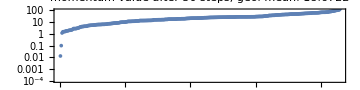

```mathematica
(* comparison with momentum, ADAM  *)
fv={};γ=0.5;α=0.0003;        (* momentum , for α=0.0004  one escapes to infinity *)
stepmom[ng_]:=(m+=γ(ng-m);θ-=α*m);                 
paths=Table[m=Table[0.,𝔇];θh={}; θ={sx,sy,sz}; (*starting position *)
Do[AppendTo[θh,θ];stepmom[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-r,r},{sy,-r,r},{sz,-r,r}];
plm=ListLogPlot[mom=Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"momentum value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

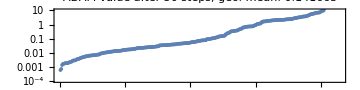

```mathematica
fv={};α=1.5;β1=0.8;β2=0.9;epsilon=10^-8.;  SeedRandom[1];            (* ADAM, tuned hyperparameters *)
stepADAM[ng_]:=(t++;m=β1*m+(1-β1)ng;vv=β2*vv+(1-β2)ng^2;
θ-=α*m/((epsilon+Sqrt[vv/(1-β2^t)])*(1-β1^t)));                 (* ADAM: https://arxiv.org/pdf/1412.6980  *)
paths=Table[m=Table[0.,𝔇];θh={};vv=0;t=0; θ={sx,sy,sz}; (*starting position *)
Do[AppendTo[θh,θ];stepADAM[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-r,r},{sy,-r,r},{sz,-r,r}];
plm=ListLogPlot[adam=Sort[fv],PlotRange->{0.0001,10},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"ADAM value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

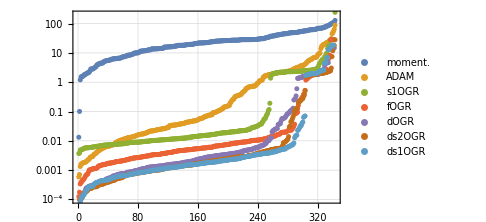

```mathematica
ListLogPlot[{mom,adam,s1OGRp,fOGRp,dOGRp,ds2OGRp,ds1OGRp},PlotRange->{0.0001,200},PlotStyle->PointSize[0.01],PlotTheme->"Detailed",ImageSize->Medium,PlotLegends->{"moment.","ADAM","s1OGR","fOGR","dOGR","ds2OGR","ds1OGR"}]
```

```mathematica
(* gathered in article: *)
```

```mathematica
(* estimate Hessian approximated as diagonal: diag(H) = dgθ/dθθ *)
dOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);      (* means *)
dθθ+=β((θ-mθ)^2-dθθ);dgθ+=β((ng-mg)*(θ-mθ)-dgθ);   (*coord.*)
θ-=1/Map[Max[#,cut]&,Abs[dgθ/dθθ]*div]*m);   (*1/|1D λ div&cut|*)
(* Hessian in gradient-based evolving d-dimensional subspace V *)
sOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);     (* means *)
V=Orthogonalize[Table[v+Γ*ng,{v,V}]]; (* explore new directions *)
pθ=V.(θ-mθ);pg=V.(ng-mg);       (* mean subtractions & projections *)
θ-=α(m-m.Transpose[V].V);       (* momentum in remaining  directions *)                                                       
mθθ+=β(KroneckerProduct[pθ,pθ]-mθθ); {e,ev}=Eigensystem[mθθ];
mgθ+=β(KroneckerProduct[pg,pθ]-mgθ); evt=Transpose[ev];
pH=evt.((ev.s[mgθ].evt)/s[Table[e,d]]).ev;   (* Hessian estimator *) 
θ-=(ma[pH].(V.m)).V);    (* 1/|~eigenvalues of pH| in local subspace*)
(*combine two above, step using w~1/2 weight mean inside the subspace: *)
dsOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);     (* means *)
dθθ+=β((θ-mθ)^2-dθθ);dgθ+=β((ng-mg)*(θ-mθ)-dgθ);(*coord.*)
V=Orthogonalize[Table[v+Γ*ng,{v,V}]];   (* explore new directions*)
pθ=V.(θ-mθ);pg=V.(ng-mg);       (* mean subtractions & projections *)                                                 
mθθ+=β(KroneckerProduct[pθ,pθ]-mθθ); {e,ev}=Eigensystem[mθθ];
mgθ+=β(KroneckerProduct[pg,pθ]-mgθ); evt=Transpose[ev];
pH=evt.((ev.s[mgθ].evt)/s[Table[e,d]]).ev;   (* Hessian estimator *) 
Δθ=eh[dgθ/dθθ]*m;θ-=Δθ-w(Δθ.Transpose[V].V-(ma[pH].(V.m)).V));
```

```mathematica
(* required eh, ma, init functions, example of application *)
eh[lm_]:=1/Map[Max[#,cut]&,Abs[lm]*div]; (* eigenvalue inv, div&cut *)
ma[A_]:=({e,ev}=Eigensystem[A];Transpose[ev].DiagonalMatrix[eh[e]].ev);
init[d_]:=(m=mg=mθ=dgθ=Table[0.,𝔇];V=RandomReal[0.001,{d,𝔇}];
dθθ=Table[1.,𝔇];mgθ=Table[0.,d,d];mθθ=IdentityMatrix[d];);
noise:=RandomReal[NormalDistribution[0,ϵ],𝔇];ϵ=0.1;   (*Gaussian noise*)
b=(1.5-x+x*y)^2+(2.25-x+x*y^2)^2+(2.625-x+x*y^3)^2;(*Beale function*)
f=Simplify[b+(b/.x->z)];v={x,y,z};𝔇=Length[v];(*3D:b(x,y)+b(z,y)*)
sub[p_]:=Table[v[[i]]->p[[i]],{i,𝔇}]; s[M_]:=M+Transpose[M];
g=Grad[f,v];H=Table[D[f,v1,v2],{v1,v},{v2,v}]; (*gradient,Hessian *)
α=0.001;β=0.6;γ=0.6;div=1.5;Γ=0.25;cut=10;     (* hyperparameters *) 
d=2; init[d]; θ={0,0,0};   (* dimension, initialize, starting position *)
steps=50;Do[sOGR[(g/.sub[θ])+noise],{i,steps}];       (* optimization *)
```

```mathematica
(* improved dOGR using corr(θ,g)=1 approxmiation (arXiv:1907.07063), λ = sqrt(dgg/dθθ) *)
```

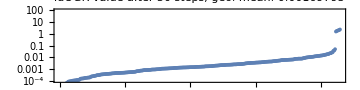

```mathematica
idOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);    (* means *)
dθθ+=β((θ-mθ)^2-dθθ);dgg+=β((ng-mg)^2-dgg); (*coord.*)
θ-=m/Map[Max[#,cut]&,Sqrt[dgg/dθθ]*div]);   (*1/|1D λ div&cut|*)

fv={};β=0.4;γ=0.5;div=1.1;cut=0.1;SeedRandom[1]; (* improvement allowed to reduce div, cut nearly nonexistant *)
paths=Table[init[𝔇];θh={};dgg=Table[0.,𝔇]; θ={sx,sy,sz};  (*starting position *)
Do[AppendTo[θh,θ];idOGR[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-r,r},{sy,-r,r},{sz,-r,r}];
ListLogPlot[dOGRp=Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"idOGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```